## Wobbling frequency for QTR model

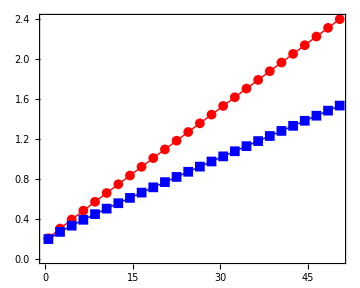

```mathematica
realspin[I_]:=Sqrt[I(I+1)];
omega[I_,j_,I1_,I2_,I3_]:=j/I3 Sqrt[(1+realspin[I]/j(I3/I1-1))(1+realspin[I]/j(I3/I2-1))];
plotdata[j_,I1_,I2_,I3_]:=Table[{spin,omega[spin,j,I1,I2,I3]},{spin,0.5,52,2}];
ListPlot[{plotdata[6.5,10,20,40],plotdata[6.5,10,30,40]},Joined->True,PlotMarkers->{Automatic, Medium},AspectRatio->0.8,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},ImageSize->Medium]
(*ListPlot[{plotdata[6.5,1,5,4],plotdata[6.5,1,6,4]},PlotRange->Full]*)
```